```mathematica
Get["C:\\Users\\Bojić\\Desktop\\faks\\5.semester\\NRO\\funkcija2.m"]
```

```mathematica
PriblizekPi[n_]:= Module[{PI, razlika},
{znotrajKroznice,znotrajKvadrata}=funkcija[n];
PI=N[4 *Length[znotrajKroznice]/n];
razlika=Abs[PI-Pi];
{PI, razlika}]
```

```mathematica
SteviloTock=10000; (*izberemo 10000 točk, ker pri 100000 je graf preveč gost*)
For[n=10,n<=SteviloTock,n*=10, 
{pi, odstopek}=PriblizekPi[n];
Print["Približek π pri "<>ToString[n]<>" točkah znaša ",pi," -> Absolutna napaka: ", odstopek];]
```

Približek π pri 10 točkah znaša 3.2 -> Absolutna napaka: 0.0584073

Približek π pri 100 točkah znaša 3.16 -> Absolutna napaka: 0.0184073

Približek π pri 1000 točkah znaša 3.18 -> Absolutna napaka: 0.0384073

Približek π pri 10000 točkah znaša 3.1528 -> Absolutna napaka: 0.0112073

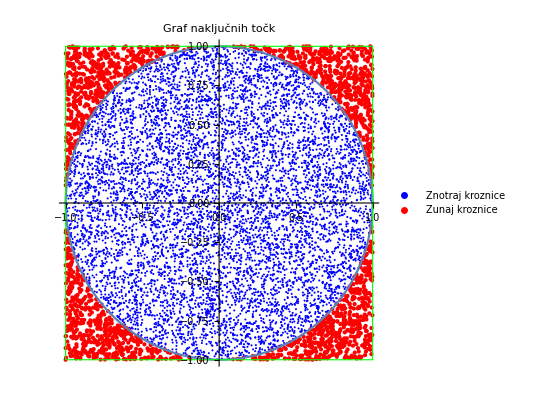

```mathematica
Graf=ListPlot[{znotrajKroznice,znotrajKvadrata},PlotLegends->{"Znotraj kroznice","Zunaj kroznice"},PlotStyle->{{Blue},{PointSize[Medium],Red}}];
kroznica=ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}];
kvadrat2=Graphics[{EdgeForm[{Dashed,Green}],FaceForm[],Rectangle[{-1,-1},{1,1}]}];
Show[Graf,kroznica,kvadrat2,AspectRatio->1,PlotLabel->"Graf naključnih točk"]
```

```mathematica
(*definiramo začetno funkcijo*)
f[t_]= Sin[t] t^2 E^-t;
(*definiramo začetni približek*)
t1=2;
(*definiramo poljubno stopnjo polinoma, do katerega bomo za začetek razvili taylorjevo vrsto*)
n=6;

(*definiramo aproksimacijsko funkcijo, ki jo dobimo z razvojem v taylorjevo vrsto začetne funkcije
pri definiranem začetnem približku in do definirane stopnje polinoma*)
app=Evaluate[Normal[Series[f[t],{t,t1,n}]]];
(*začetno funkcijo in njeno aproksimacijo narišemo v en graf*)
Plot[{f[t],app},{t,0,4},AxesLabel->{"t","f(t)"}, PlotLabel->"Aproksimacija z razvojem Taylorjeve vrste", 
PlotLegends->{"Začetna funkcija", "Aproksimacija s polinomom reda 6"}];

(*Sedaj še razširimo funkcijo z opcijo manipulate*)
Manipulate[app=Evaluate[Normal[Series[f[t],{t,t1,red}]]]; Plot[{f[t],app},{t,0,4}, PlotLegends->{"Začetna funkcija","Aproksimacija s polinomom reda "<>ToString[red]<>""},PlotLabel->"Aproksimacija z razvojem Taylorjeve vrste",AxesLabel->{"t","f(t)"}],
 (*Drsnik za spreminjanje reda približka*)
 {{red,1,"Red polinoma:"},1,10,1}]
```